```mathematica
Integrate[Cos[n x]Cos[x],{x,0,π}]
Assuming[n∈Integers,Integrate[Cos[n x]Cos[x],{x,0,π}]]
```

-(n Sin[n π])/(-1+n^2)

0

α

4/25

0

2 Vinf (4/25 √(1-(1-2 x)^2)+α/(√(1-(1-2 x)^2))+((1-2 x) α)/(√(1-(1-2 x)^2)))

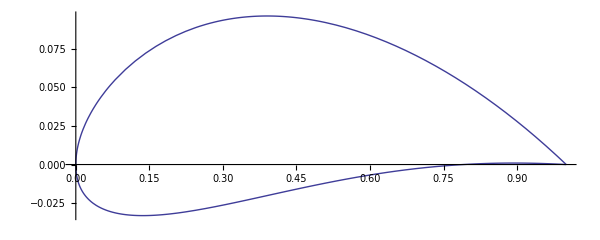

```mathematica
(* Problem 1 *)
eps=4/100;
p=5/10;
c=1;
τ=12/100;
(*α=4 π/180;*)
T[x_]=10 τ c(0.2969 √(x/c)-0.126(x/c)-0.3537(x/c)^2+0.2843(x/c)^3-0.1015(x/c)^4);
Y[x_]=Piecewise[{{(eps x)/p^2(2 p - x/c), 0 ≤ x/c ≤ p },{(eps(c-x))/(1-p)^2(1+x/c-2p) ,p < x/c ≤ 1 }}];
s[θ_]=Simplify[D[Y[x],x]/.x->c/2(1-Cos[θ])];
A0[α_]=Simplify[α-1/π Integrate[s[θ],{θ,0,π}]]
A1=Simplify[2/π Integrate[Cos[θ]s[θ],{θ,0,π}]]
Am[m_]=Assuming[m∈Integers,Simplify[2/π Integrate[Cos[m θ]s[θ],{θ,0,π}]]]
g[θ_,α_]=Simplify[2 Vinf(A0[α](1+Cos[θ])/Sin[θ]+A1 Sin[θ]+Sum[Am[n],{n,2,∞}])];
gx[x_,α_]=g[ArcCos[1-2 x/c],α]
qx[x_]=Vinf D[T[x]/2,x];
(* Plot airfoil *)
Plot[Y[x]+{T[x]/2,-T[x]/2},{x,0,1},AspectRatio->Automatic,ImageSize->600]
Manipulate[Plot[{1-(Vinf+1/2 gx[x,α π/180])^2/Vinf^2-(1/2 qx[x]^2)/Vinf^2,1-(Vinf-1/2 gx[x,α π/180])^2/Vinf^2},{x,0,1}],{{α,0},-4,4}]
```

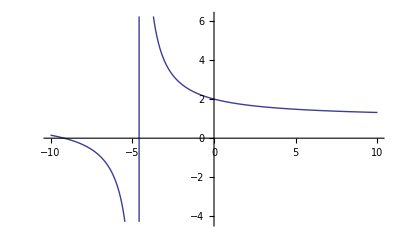

```mathematica
Plot[(4/25+α π/180)/(2/25+α π/180),{α,-10,10}]
```

```mathematica
Plot[gx[x],{x,0,1}]
```

-Graphics-

```mathematica
dT[x_]=D[T[x],x]
uu[x_]=Assuming[0<x<c,1/(√(1+(dT[x]/2)^2))Integrate[dT[xp]/(x-xp),{xp,0,c}]]
```

6/5 (-0.126+0.14845/(√x)-0.7074 x+0.8529 x^2-0.406 x^3)

((0.-1.11929 ⅈ)+√x (0.49954+x ((-0.77988-4.44089×10^-16 ⅈ)+((0.4872+4.44089×10^-16 ⅈ)-(0.+2.22045×10^-16 ⅈ) x) x))-0.17814 Log[1.-1. √x]+0.17814 Log[1.+1. √x]+√x ((0.1512+x (0.84888+(-1.02348+0.4872 x) x)) Log[1.-1. x]+(-0.1512+x (-0.84888+(1.02348-0.4872 x) x)) Log[x]))/(√x √(1+9/25 (-0.126+0.14845/(√x)-0.7074 x+0.8529 x^2-0.406 x^3)^2))

```mathematica
uu[0.5]
```

0.675485-1.58291 ⅈ

```mathematica
(* Plot Cp *)

(*Plot[{gx[x],qx[x]}/Vinf,{x,0,1}]*)
(*vtPlus[x_]=1/2 qx[x];
ut[x_]=Assuming[0<x<1,Simplify[1/(2π)Integrate[qx[xp] 1/(x-xp),{xp,0,1}]]]
ut[x_]=Assuming[0<x<1,Simplify[1/(2π)Integrate[qx[xp] 1/(x-xp),{xp,0,1}]]]
vtMinus[x_]=-vtPlus[x];*)
ut[x_]=Vinf +Vinf*Assuming[0<x<1,Simplify[1/(2π)Integrate[D[1/2 T[xp],xp] 1/(x-xp),{xp,0,1}]]]
ucPlus[x_]=1/2 gx[x];
ucMinus[x_]=-ucPlus[x];
vc[x_]=Assuming[0<x<1,Simplify[-1/(2π)Integrate[gx[xp] 1/(x-xp),{xp,0,1}]]]
```

Vinf+1/(2 π √x)Vinf ((0.-0.559643 ⅈ)+√x (0.24977+x ((-0.38994-2.22045×10^-16 ⅈ)+((0.2436+2.22045×10^-16 ⅈ)-(0.+1.11022×10^-16 ⅈ) x) x))-0.08907 Log[1.-1. √x]+0.08907 Log[1.+1. √x]+√x ((0.0756+x (0.42444+(-0.51174+0.2436 x) x)) Log[1.-1. x]+(-0.0756+x (-0.42444+(0.51174-0.2436 x) x)) Log[x]))

1/25 Vinf (4-8 x+8 ⅈ √(-(-1+x) x)+25 ⅈ (ⅈ+√(-1+1/x)) α)

```mathematica
Plot[ut[x]/Vinf/.α->0 π/180,{x,0,1}]
```

-Graphics-

```mathematica
Assuming[{Vinf>0, 0<x<1},Simplify[1-((vtPlus+vc)^2-(ut+ucPlus)^2)/Vinf^2]]
```

```mathematica
Simplify[gx[xp] 1/(x-xp)]
Assuming[{Vinf>0,0<x<1},Simplify[1/(2π)Integrate[Simplify[gx[xp] 1/(x-xp)],{xp,0,1}]]]
```

(16 Vinf √(-(-1+xp) xp))/(25 (x-xp))

```mathematica
Plot[(ut+ucPlus)^2+(vtPlus+vc)^2
```

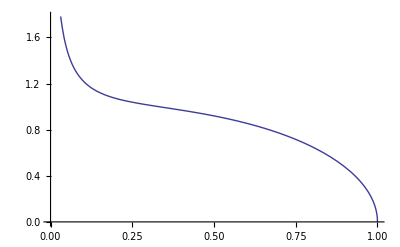

```mathematica
Plot[Simplify[2/Vinf(g[ArcCos[1-2 x/c]]/.eps->4/100/.p->5/10/.c->1/.α->4 π/180)],{x,0,1}]
```

```mathematica
Cl=Assuming[0<p<1,Simplify[2π(A0+A1/2)]];
Cmac=Assuming[0<p<1,Simplify[-π/4(A1-Am[2])]];
xcp=Assuming[0<p<1,Simplify[c/4((A0+A1-1/2 Am[2])/(A0+1/2 A1))]];
```

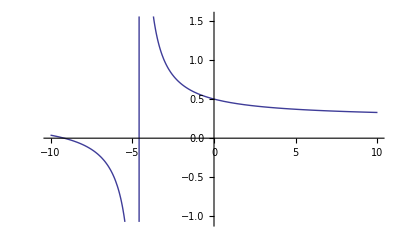

```mathematica
Plot[Simplify[xcp/c/.eps->4/100/.p->5/10/.α->αDeg π/180],{αDeg,-10,10}]
```

```mathematica
cps=Assuming[0<p<1,FullSimplify[4(A0 Cot[θ/2]+A1 Sin[θ]+Sum[Am[n]Sin[n θ],{n,2,∞}])]]
```

$Aborted

```mathematica
Plot[cps/.eps->4/100/.p->5/10/.x->ArcCos,{θ}
```

```mathematica
Integrate[(p-1/2(1-Cos[θp])),θp]
Integrate[Cos[m θp](p-1/2(1-Cos[θp])),θp]
```

-θp/2+p θp+Sin[θp]/2

Sin[(-1+m) θp]/(4 (-1+m))-Sin[m θp]/(2 m)+(p Sin[m θp])/m+Sin[(1+m) θp]/(4 (1+m))